# Mathematica的矩阵运算

## 一.矩阵的特征值分解 M = ξuξ^-1

1. 矩阵分布
这里的 m1 为了直观可以转置一下, 因为 MMA 里面一个特征向量是一个列表，所以每一个特征向量是一个行向量

2. 点积的计算方法
P*Q*P^-1 这个MMA语法是错误的，这个是对应元素的乘积
注：Mathematica 里边的矩阵乘法要计算点积
必须使用 Dot 函数, 比如 dot[A, B], 不能直接A*B

```mathematica
M = {{0, 1}, {1, 1}};
EigVecM1 = Eigenvectors[M];
EigValM1 = Eigenvalues[M];

(*Dot[Dot[EigVecM, EigValM], EigVecM//Inverse]; 错误的代码：特征值需要对角化为一个矩阵*)
Dot[Dot[EigVecM, EigValM//DiagonalMatrix], EigVecM//Inverse]//Simplify//MatrixForm
```

(0 | 1
1 | 1)

### 1. 查看MMA中特征向量和特征值的分布与对应关系

```mathematica
EigVecM1//MatrixForm
EigValM1//MatrixForm
```

(1/2 (-1+√5) | 1
1/2 (-1-√5) | 1)

(1/2 (1+√5)
1/2 (1-√5))

### 2. 假如我们一定要转置

我们就必须按照下面的语法：推导过程如下：

m = PQP^-1 ⟶ m^T = (PQP^-1)^T=(P^-1)^T Q^T P^T
所以这里的结果相同, 只是是因为 m=m^T

```mathematica
M = {{0, 1}, {1, 1}};
EigVecM1 = Eigenvectors[M]//Transpose;
EigValM1 = Eigenvalues[M]//Transpose;
Dot[Dot[EigVecM1//Inverse//Transpose, EigValM1//DiagonalMatrix//Transpose], EigVecM1//Transpose]//Simplify//MatrixForm
```

(0 | 1
1 | 1)

### 3. 检验矩阵的特征值分解

下面这个是正确的分解结果， 我们输入了正确的矩阵 P, Q

```mathematica
P = {{1/2*(-1-Sqrt[5]), 1/2*(-1+Sqrt[5])}, {1, 1}};
Q = {{1/2*(1-Sqrt[5]), 0}, {0, 1/2*(1+Sqrt[5])}};

z = Dot[Dot[P, Q], Inverse[P]];
z//Simplify//MatrixForm
```

(0 | 1
1 | 1)

## 二.斐波那契数列

### 1. 第一种斐波那契数列通项公式

-Graphics-

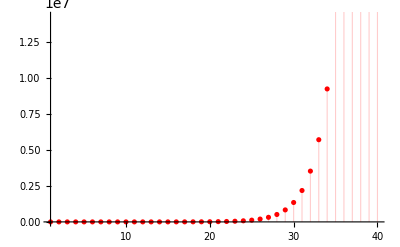

```mathematica
num = Sqrt[5];
formular = 2^(-k)/(num+5)(num*(1+num)^k + 3*(1+num)^k + 2*(-num+1)^k);
(* 绘制负半轴的情况 *)
dots = Table[formular, {k, -100, 100}];
ListPlot[dots]
DiscretePlot[formular, {k, 1, 40}, PlotStyle->{Red, Thickness[0.002]}]
```

### 2. 第二种斐波那契数列通项公式

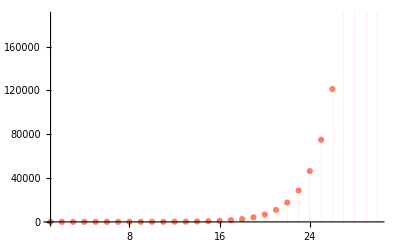

```mathematica
(*斐波那契数列的如下通项公式*)
g[n_]:= 1/(√5)(((1+√5)/2)^n-((1-√5)/2)^n);

DiscretePlot[
	FullSimplify[g[n]], {n, 1, 30},
	PlotStyle->Directive[
		RGBColor[1, 0.49, 0.39],
		Opacity[1],
		AbsoluteThickness[0]
	]
]
```